```mathematica
(* MA39110 / Assignment 12 / 16MA20053 / NER ROHIT *)
ClearAll["Global`*"];
```

```mathematica
Thomas[a_,b_,c_,d_]:=Module[{c1=Range[Length[c]],d1=Range[Length[d]],x=Range[Length[b]]},
c1[[1]]=c[[1]]/b[[1]]; d1[[1]]=d[[1]]/b[[1]];
Do[
If[i≠Length[d],c1[[i]]=c[[i]]/(b[[i]]-a[[i-1]]*c1[[i-1]])];
d1[[i]]=(d[[i]]-a[[i-1]]*d1[[i-1]])/(b[[i]]-a[[i-1]]*c1[[i-1]]);
,{i,2,Length[d]}];
x[[Length[b]]]=d1[[Length[b]]];
Do[
x[[i]]=d1[[i]]-c1[[i]]*x[[i+1]];
,{i,Length[b]-1,1,-1}];
x];
Model[n0_,k0_,t0_]:=Module[{n=n0*10,k=k0,t=t0},
x0=0;xf=10;h=(xf-x0)/n;
X=Table[x0+x*h,{x,1,n-1}];
XT=Table[x0+x*h,{x,0,n}];
A=Table[0,{x,1,n-1},{y,1,n-1}];
B=Table[0,{x,1,n-1}];
nu=0.5;
s=nu*k/h^2;
f[x_]=Piecewise[{{x,0≤x≤1},{0,x<0},{0,x>1}}];
U=Table[f[XT[[x]]],{x,1,n+1}];
UT=U;
PLT=Table[0,{x,1,t}];
For[j=1,j≤t,j++,{
U=UT;
For[i=1,i<n,i++,
{
im=i+1;
A[[i,i]]=1+s;
B[[i]]=0.5s*U[[im-1]]+(1-s)U[[im]]+s*U[[im+1]]/2;
If[i≠1,A[[i,i-1]]=-k*U[[im-1]]/(4h)-s/2];
If[i≠n-1,A[[i,i+1]]=k*U[[im+1]]/(4h)-s/2];
}];
UT=U+N[Flatten[{{0},Thomas[Diagonal[A,-1],Diagonal[A],Diagonal[A,1],B],{1}}]];
PLT[[j]]=ListLinePlot[Transpose[{XT,U}],PlotRange->{0,1000}];
}];
PLT
];
```

```mathematica
(*Manipulate[Model[10,0.2,Floor[t]],{t,1,100}]*)
```

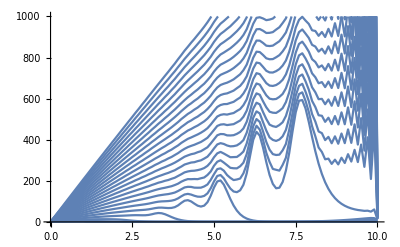

```mathematica
Show[Model[10,0.2,50][[1;;;;2]]]
```

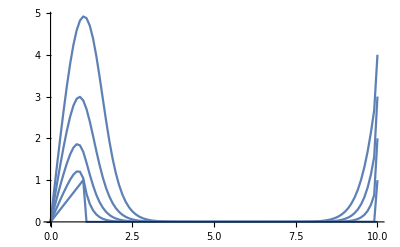

```mathematica
Show[Model[10,0.2,50][[1;;5;;1]],PlotRange->Automatic]
```